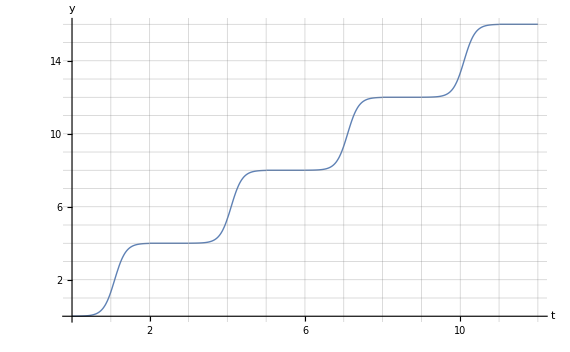

```mathematica
G[x_]:=4/(1+2Exp[-7(x-1)])
F[x_]:=Piecewise[{{G[x],0<=x<=2},{4,2≤x≤3},{G[x-3]+4,3<x≤5},{8,5<x≤6},{G[x-6]+8,6<x≤8},{12,8<x≤9},{G[x-9]+12,9<x≤11},{16,11<x≤12}}]
Plot[F[x],{x,0,12},AxesLabel->{"t","y"},GridLines->{{-2,-1,0,1,2,3,4,5,6,7,8,9,10,11,12},{-2,-1,0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16}},Ticks->{{2,6,10},{2,6,10,14}},PlotStyle->{Thick}]
```